## Online supplementary material to SVOČ 2024 thesis

### Mendroš, E. (2024). Bivariate Simplicial Depth: Explicit Expression, Computation and Applications

#### (a) Supporting procedures within the main algorithm

An auxiliary in-build function which finds all intersections between two line segments.
Input: Two pairs of points in the plane in general position a={A1, A2},  b={B1, B2}.
Output: Intersection point of the two line segments with endpoints A1, A2 and B1, B2. If none, returns an empty set.

```mathematica
Intersect[a_,b_]:=Graphics`Mesh`FindIntersections[{Line[a],Line[b]}]
```

An auxiliary function which computes the sample simplicial depth of a given point x with respect to  a given dataset X.
Input: Two-dimensional point x and a list of two-dimensional points X.
Output: Sample simplicial depth of x with respect to X.

```mathematica
DepthSD[X_, x_]:=Module[{data,alt,y,cts0,cts1,n,i},
data = X-ConstantArray[x,Length[X]];
alt=UnitStep[data[[All,1]]];
y=Ordering[data[[All,2]]/data[[All,1]]];
y=alt[[y]];
cts0={1,0,0,0};
cts1={1,0,0,0};
n=Length[y];
For[i=1,i<=n,i++,If[y[[i]]==0,cts0[[2;;4]]=cts0[[2;;4]]+cts1[[1;;3]],cts1[[2;;4]]=cts1[[2;;4]]+cts0[[1;;3]]]];
res=cts1[[4]]+cts0[[4]];
Return[res];]
```

An auxiliary function which computes the sample simplicial depth of a given set of points x with respect to  a given dataset X.
Input: List of two-dimensional points x and a list of two-dimensional points X.
Output: Sample simplicial depth of each point in x with respect to X.

```mathematica
DepthSDVec[X_,x_]:=Table[DepthSD[X,x[[j]]],{j,1,Length[x]}]
```

#### (b) The main algorithm: Determination of the exact sample SD of the entire plane (Section 4.2)

Input: List of two-dimensional points X.
Output: List of faces (represented by its vertices),  a list of the corresponding representative points, a list of  the corresponding depths, and a list of opacities (for plotting).

```mathematica
PlaneSD[X_]:=Module[{S,edge={},edges={},sorted,graph,planarGraph,faces,means,depth,opacities},
S=Subsets[X,{2}];
Do[Do[edge=Union[edge,N[Intersect[S[[i]],S[[j]]],8]],{j,Range[Length[S]]}];
sorted=Sort[edge,#1<#2&];
edge={};
Do[AppendTo[edges,{sorted[[k]],sorted[[k+1]]}],{k,Range[Length[sorted]-1]}],{i,Range[Length[S]]}];
graph=Graph[UndirectedEdge@@@edges];
planarGraph=PlanarGraph[graph];
faces=PlanarFaceList[planarGraph];
faces = Rest[faces];(*Delete the outer face*)
(*means=Mean/@faces;*)
means=Mean/@(Take[#,3]&/@faces);
depth=DepthSDVec[X,means];opacities=Rescale[Join[depth,{0}]];
{faces,means,depth,opacities}]
```

#### (c) Dataset from Figures 16 and 17 in Section 4.2

Define the dataset of n=20 points.

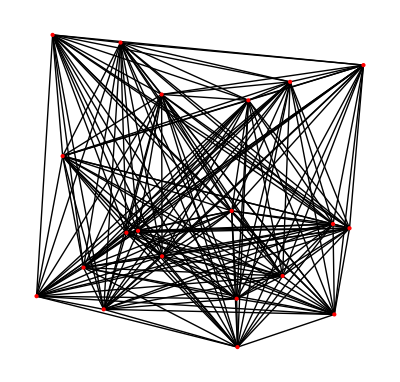

```mathematica
X={{-2.2565653343611913,-3.39671342426729},{5.3977511304809696,7.047880791248673},{7.962328155307553,-1.460470087421104},{4.949837331597678,-4.574060332184079},{-8.800627651101784,9.859798987992235},{-4.388440523881009,-1.9846791532065353},{-9.760678552209882,-5.785341419036357},{-6.9530124213997055,-4.073531657749548},{8.04309785278037,-6.877451947927412},{-4.74030719476648,9.399102729077903},{2.251859347960689,-8.833157791008158},{1.9039105071462181,-0.680842353488682},{8.949773481510881,-1.7159113040399454},{-8.199055325255479,2.603061578811534},{-5.748205389968906,-6.571918310112839},{-3.6936902918749297,-1.8726123555741268},{2.902616145292157,5.9417284163061055},{-2.2843035817777206,6.294777855556248},{2.2029651240586716,-5.939082846575019},{9.783066120563,8.050859728981841}};
S=Subsets[X,{2}];
Graphics[{Black,Line/@S,Red,PointSize[Large],Point[X]}]
```

```mathematica
{faces,means,depth,opacities}=PlaneSD[X];
```

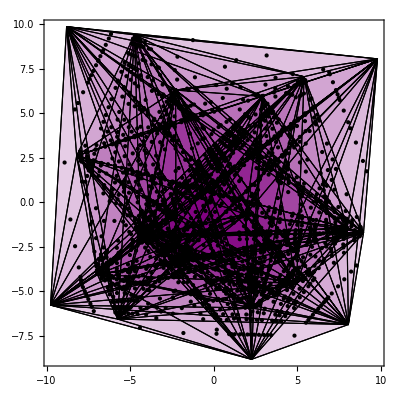

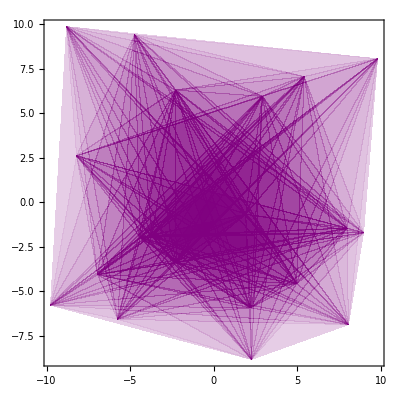

```mathematica
Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],EdgeForm[{Thin,Black}],Polygon[faces[[i]]]},{i,Length[faces]}],PointSize[Small],Point[means]},Frame->True,PlotRangePadding->0.1,AspectRatio->1]
Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,PlotRangePadding->0.1,AspectRatio->1]
```

#### (d) Level sets in Figures 27 - 32 from Appendix G

```mathematica
quantiles=Table[Quantile[depth,i/10],{i,1,9}];
quantiles = Flatten[AppendTo[quantiles, {315, 320, 325}]];
```

```mathematica
levelset=Flatten[Position[depth,_?(#>quantiles[[1]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[2]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[3]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[4]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[5]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[6]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[7]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[8]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[9]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[10]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[11]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[12]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
medians=Flatten[Position[depth,Max[depth]]];
Graphics[Table[{FaceForm[Purple],EdgeForm[{Thin,White}],Polygon[faces[[medians[[i]]]]]},{i,Length[medians]}],Frame->True,PlotRange->{{-1.5,0.5},{-2.5,-0.5}},AspectRatio->1]
```

#### (e) Counterexample 1: Five disjoint median faces that are not in the center of rotational symmetry.

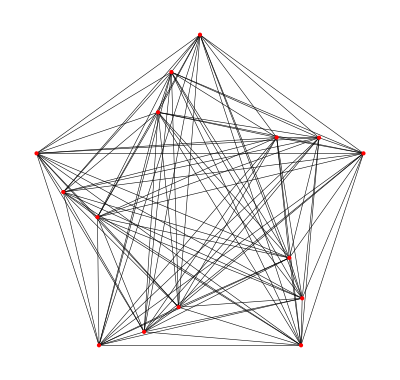

```mathematica
X1=Table[{10Cos[2*Pi*k/5 +Pi/2], 10Sin[2*Pi*k/5+Pi/2]},{k,0,4}];
X2=Table[{8Cos[2*Pi*k/5+Pi/5 *1/3+Pi/2],8Sin[2*Pi*k/5+Pi/5 *1/3+Pi/2]},{k,0,4}];
X3=Table[{6Cos[2*Pi*k/5+Pi/5 *2/3+Pi/2],6Sin[2*Pi*k/5+Pi/5 *2/3+Pi/2]},{k,0,4}];
X=Join[X1,X2,X3];
S=Subsets[X,{2}];
Graphics[{Black,Thickness[0.001],Line/@S,Red,PointSize[Large],Point[X]}]
```

```mathematica
{faces,means,depth,opacities}=PlaneSD[X];
```

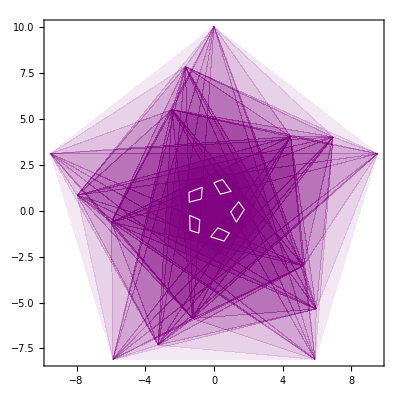

```mathematica
medians=Flatten[Position[depth,Max[depth]]];
Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thin,White}],Polygon[faces[[medians[[i]]]]]},{i,Length[medians]}],Frame->True,AspectRatio->1]]
```

#### (f) Counterexample 2: Median face “far” from the center and a level set with a “hole”.

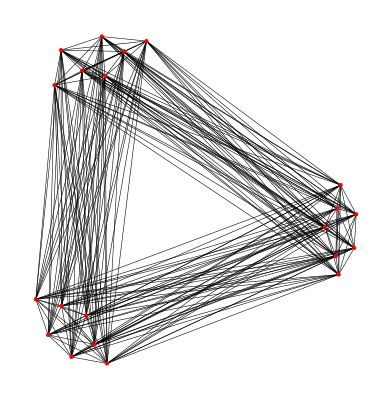

```mathematica
X={{-3.522201231367931,3.1094933498719075},{-3.34833789444781,4.04835536924056},{-2.2529988718510476,4.413468376772814},{-1.053341847102213,4.2917640409287285},{-3.696064568288052,-3.58424512155275},{-3.0701565553756156,-4.175380467081161},{-2.1139082023149505,-4.349243804001282},{-4.026404908436281,-2.627996768492085},{-2.6702708804593382,-3.062655110792387},{-2.166067203390987,3.352902021560076},{4.11039925942538,-1.9673160881956238},{4.52767126803367,-1.2544764068231289},{4.579830269109706,-0.3503870548385002},{4.162558260501417,0.431997961302044},{3.745286251893125,-0.698113728678742},{-1.6572727001218097,4.013309180391115},{-3.337108223739135,-2.806400445363499},{-2.449647947111114,-3.836488266449595},{-2.7824455508466217,3.500906520671365},{4.063676583140968,-0.19156213029879415},{4.031981573261396,-1.4752100304214681}};
S=Subsets[X,{2}];
Graphics[{Black,Thickness[0.001],Line/@S,Red,PointSize[Large],Point[X]}]
```

```mathematica
{faces,means,depth,opacities}=PlaneSD[X];
```

Notice the median face (tiny white area) in the bottom left corner of the  figure below.

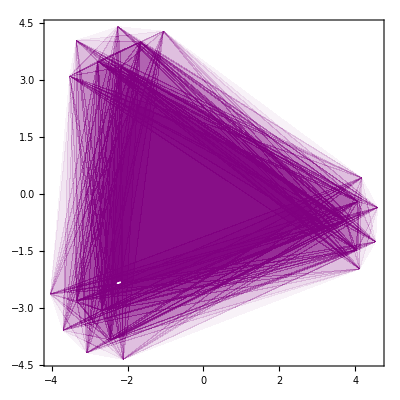

```mathematica
medians=Flatten[Position[depth,Max[depth]]];
Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thin,White}],Polygon[faces[[medians[[i]]]]]},{i,Length[medians]}],Frame->True,AspectRatio->1]]
```

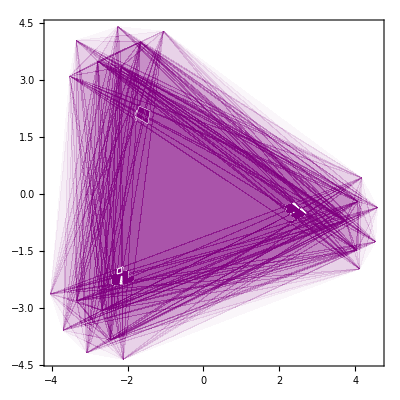

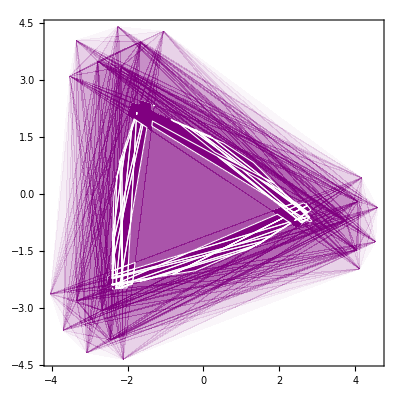

```mathematica
levelset=Flatten[Position[depth,_?(#>358&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>350&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
```

#### (g) Counterexample 3

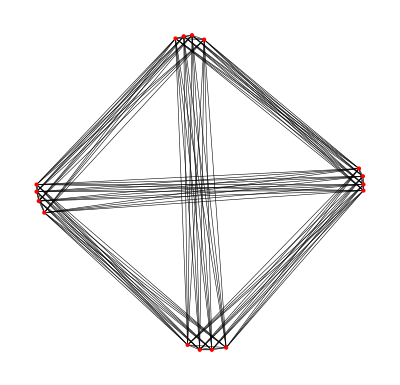

```mathematica
X={{-0.7698124234937884,4.283213810878507},{-0.5320998493969986,4.346603830637653},{-0.29438727530020703,4.378298840517225},{0.054257833375088715,4.2515188009989355},{-4.763383668319884,0.08362500183519328},{-4.763383668319884,-0.1223925623820247},{-4.699993648560739,-0.39180014635838945},{-4.541518599162878,-0.7245977500938965},{-0.42116731481849445,-4.52799893564256},{-0.07252220614320048,-4.670626480100634},{0.2761229025320935,-4.670626480100634},{0.688158030966532,-4.607236460341491},{4.507406721454979,0.5432026450889909},{4.618339256033481,0.32133757593198464},{4.634186760973268,0.08362500183519328},{4.634186760973268,-0.09069755250245282}};
S=Subsets[X,{2}];
Graphics[{Black,Thickness[0.001],Line/@S,Red,PointSize[Large],Point[X]}]
```

```mathematica
{faces,means,depth,opacities}=PlaneSD[X];
```

```mathematica
quantiles=Table[Quantile[depth,i/10],{i,1,9}]
quantiles = Flatten[AppendTo[quantiles, {155, 160, 162, 166}]];
Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],EdgeForm[{Thin,Black}],Polygon[faces[[i]]]},{i,Length[faces]}],PointSize[Small],Point[means]},Frame->True,PlotRangePadding->0.1,AspectRatio->1]
levelset=Flatten[Position[depth,_?(#>quantiles[[1]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[2]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[3]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[4]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[5]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[6]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[7]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[8]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[9]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[10]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[11]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
levelset=Flatten[Position[depth,_?(#>quantiles[[12]]&)]];Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/1.4,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thick,White}],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1],
Graphics[Table[{FaceForm[Purple],Polygon[faces[[levelset[[i]]]]]},{i,Length[levelset]}],Frame->True,AspectRatio->1]]
medians=Flatten[Position[depth,Max[depth]]];
Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]]/2,Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thin,White}],Polygon[faces[[medians[[i]]]]]},{i,Length[medians]}],Frame->True,AspectRatio->1]]
```

{50,66,78,90,104,114,126,140,152}

#### (h) Define your own dataset

Choose data points by clicking on the grid below. Then execute the code below the grid to compute and plot the exact sample SD .

```mathematica
X={};
DynamicModule[{},EventHandler[Dynamic@Graphics[{Point[Dynamic[X]],Red,PointSize[Large],Dynamic@Point@MousePosition["Graphics"],Gray,Line[{{#,-5},{#,5}}]&/@Range[-5,5],Line[{{-5,#},{5,#}}]&/@Range[-5,5]},PlotRange->{{-5,5},{-5,5}},Frame->True],{"MouseClicked":>(AppendTo[X,MousePosition["Graphics"]])}],Initialization:>(X={})]
```

```mathematica
{faces,means,depth,opacities}=PlaneSD[X];
```

```mathematica
Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],EdgeForm[{Thin,Black}],Polygon[faces[[i]]]},{i,Length[faces]}],PointSize[Small],Point[means]},Frame->True,PlotRangePadding->0.1,AspectRatio->1]
medians=Flatten[Position[depth,Max[depth]]];
Show[Graphics[{Table[{FaceForm[Opacity[opacities[[i]],Purple]],Polygon[faces[[i]]]},{i,Length[faces]}]},Frame->True,AspectRatio->1] ,Graphics[Table[{FaceForm[Purple],EdgeForm[{Thin,White}],Polygon[faces[[medians[[i]]]]]},{i,Length[medians]}],Frame->True,AspectRatio->1]]
```